```mathematica
Clear[ω];
Clear[κ];
Clear[q];
$Assumptions={κ>0,ω>0,q∈Reals};
gauFourier=Integrate[-(2*ω)/(√π)*(2*π)/(I*q)*r*(Exp[I*q*r-1/3*(ω*r)^2]-Exp[-I*q*r-1/3*(ω*r)^2]),{r,0,∞}]
expFourier=Integrate[(2*π)/(I*q)*r*(Exp[I*q*r-ω*r]-Exp[-I*q*r-ω*r]),{r,0,∞}]
```

-(6 √3 ⅇ^(-(3 q^2)/(4 ω^2)) π)/ω^2

(8 π ω)/((q^2+ω^2)^2)

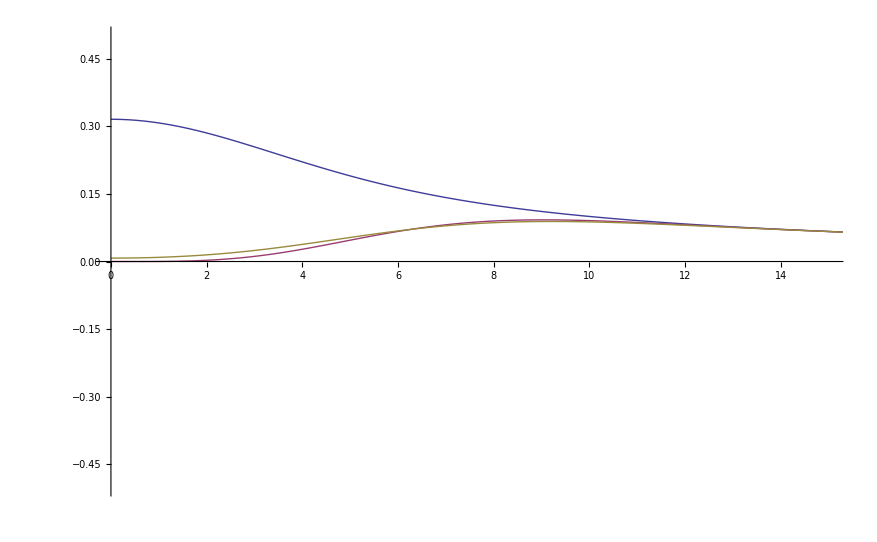

```mathematica
ω=1.0/3.0;
τA=2.0;
τB=2.0;
κ=50.0;
γABlrExact[ω_,x_]:=1/(2*π)^2*(τA^4*τB^4)/x*2*Quiet[NIntegrate[Sin[q*x]/(q*(q^2+τA^2)^2*(q^2+τB^2)^2)*(4*π*Exp[-q^2/(4*ω^2)]),{q,0,∞}]];
γABlrApprox[ω_,x_]:=1/x*Erf[ω*x]*Erf[x];
γABlrApprox[ω_,x_]:=1/x*Erf[x]*(Erf[ω*x]-(2*ω)/(√π)*x*Exp[-1/3*(ω*x)^2]);
γABlrGauss[ω_,x_]:=1/(2*π)^2*(τA^4*τB^4)/x*2*Quiet[NIntegrate[q*Sin[q*x]/((q^2+τA^2)^2*(q^2+τB^2)^2)*(-(6 √3 ⅇ^(-(3 q^2)/(4 ω^2)) π)/ω^2),{q,0,∞}]];
γABlrYukawa[ω_,x_]:=1/(2*π)^2*(τA^4*τB^4)/x*2*Quiet[NIntegrate[q*Sin[q*x]/((q^2+τA^2)^2*(q^2+τB^2)^2)*(4*π*(1/q^2-1/(q^2+ω^2))),{q,0,∞}]];
rs=Range[0.000001, 20.0, 0.1];
γABlrExactLine[ω_]:=Map[{#,γABlrExact[ω,#]}&,rs];
γABlrApproxLine[ω_]:=Map[{#,γABlrApprox[ω,#]}&,rs];
γABlrGaussLine[ω_]:=Map[{#,γABlrGauss[ω,#]}&,rs];
γABlrYukawaLine[ω_]:=Map[{#,γABlrYukawa[ω,#]}&,rs];
γABlrExactGaussLine[ω_]:=Map[{#,γABlrExact[ω,#]+γABlrGauss[ω,#]}&,rs];
ListLinePlot[{
γABlrExactLine[ω],γABlrApproxLine[ω],γABlrExactGaussLine[ω]
},PlotRange->{{0,15},{-0.5,0.5}}]
```

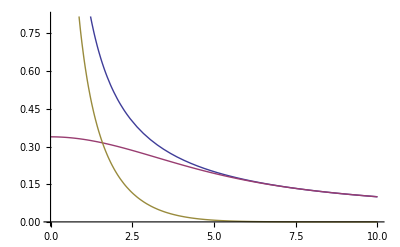

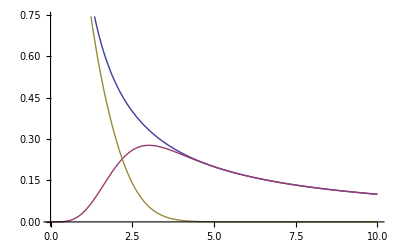

((2 DawsonF[q/(2 ω)])/(√π)-ⅇ^(-q^2/(4 ω^2)) (-2 ⅈ+Erfi[q/(2 ω)]))/(√(2 π) q)

```mathematica
switchErf[x_]:=Erf[ω*x];
switchErfGauss[x_]:=Erf[ω*x]-(2*ω)/(√π)*x*Exp[-1/3*(ω*x)^2];
ω=0.3;
Plot[{1/x,switchErf[x]/x,(1-switchErf[x])/x},{x,0,10}]
ω=1.0;
Plot[{1/x,switchErfGauss[x]/x,(1-switchErfGauss[x])/x},{x,0,10}]
Clear[ω];
FourierTransform[Erf[ω*x],x,q]
```

```mathematica
Manipulate[Plot[{Abs[((2 DawsonF[q/(2 ω)])/(√π)-ⅇ^(-q^2/(4 ω^2)) (-2 ⅈ+Erfi[q/(2 ω)]))/q],2/q*Exp[-q^2/(4*ω^2)]},{q,0,10}],{ω,1,10}]
```

```mathematica
FourierTransform[√(2*π)*(-2*ω*x)/(√π)*Exp[-1/3*(ω*x)^2],x,q]
```

-(3 ⅈ √3 ⅇ^(-(3 q^2)/(4 ω^2)) q)/ω^2

```mathematica
$Assumptions={σ>0};
Integrate[r*Exp[-r^2/(2*σ^2)]*(Exp[I*q*r]-Exp[-I*q*r]),{r,0,∞}]
```